Soliton Modulation Theory: Hodograph Method

```mathematica
ClearAll["Global`*"]
```

Functions for T=t/w and Y=y/w

```mathematica
T[Rp_,Rm_]:=3*(1+Rp*Rm)/(Rp+Rm)^3
```

```mathematica
Y[Rp_,Rm_]:=1/2*(Rm-Rp)*(Rp^2-4*Rp*Rm+Rm^2-6)/(Rp+Rm)^3
```

```mathematica
Tp[a0_,Rm_]:=T[2*Sqrt[a0]-1,Rm]
Yp[a0_,Rm_]:=Y[2*Sqrt[a0]-1,Rm]
Tm[a0_,Rp_]:= T[Rp,2*Sqrt[a0]-1]
Ym[a0_,Rp_]:= Y[Rp,2*Sqrt[a0]-1]
```

```mathematica
a0 = 0.75;
```

Post refers to what happens when either R+ or R- varies, and the other stays constant at 2 √a-1

```mathematica
Post = ParametricPlot[{{Tp[a0,R],Yp[a0,R]},{Tm[a0,R],Ym[a0,R]}},{R,2*Sqrt[a0]-1,1}];
```

```mathematica
Solve[Y==1/2+2*T-4*Sqrt[3*T]/3,T]
```

{{T→1/12 (5+6 Y-4 √(1+6 Y))},{T→1/12 (5+6 Y+4 √(1+6 Y))}}

```mathematica
Mid = Plot[1/12 (5+6 Y-4 √(1+6 Y)),{Y,3/4,1}];
```

Pre refers to what happens before the two simple waves interact, and can be found directly from Whitham theory

```mathematica
Pre = Plot[{Y*2/3-0.5,Y*-2/3+0.5},{Y,0,3/4}];
```

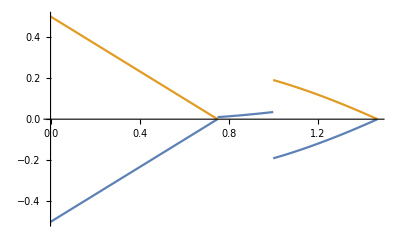

```mathematica
Show[Pre,Mid,Post,PlotRange->All]
```